```mathematica
(*importing all the data available from Kaggle*)
fulldata=Import["C:\\Users\\rbc15\\Desktop\\Minerva\\first year\\classes\\second semester\\Formal Analysis\\Assignments\\flavors_of_cacao.csv"]
```

{{Company 
(Maker-if known),Specific Bean Origin
or Bar Name,REF,Review
Date,Cocoa
Percent,Company
Location,Rating,Bean
Type,Broad Bean
Origin},{A. Morin,Agua Grande,1876,2016,63%,France,3.75, ,Sao Tome},1793,{Zotter,Brazil, Mitzi Blue,486,2010,65%,Austria,3, ,Brazil}}
 |  |  |  |

```mathematica
(*because I am only interested in the country of origin and the rating for now, I will only import those two data columns and delete the headings*)
```

```mathematica
cutdata= fulldata[[2;;-1,6;;7]]
```

{{France,3.75},{France,2.75},{France,3},{France,3.5},{France,3.5},{France,2.75},{France,3.5},{France,3.5},{France,3.75},{France,4},1776,{Austria,3.25},{Austria,3.75},{Austria,3.25},{Austria,3.5},{Austria,3.75},{Austria,3},{Austria,3.5},{Austria,3.25},{Austria,3}}
 |  |  |  |

```mathematica
(*associate each country with a list of its chocolate ratings*)
associateddata=GroupBy[cutdata,First-> Last]
```

```mathematica
(*get a list of all the countries that have at least a sample size of 20*)
```

```mathematica
keys= Keys[Select[Map[Length,associateddata],#>19&]]
```

{France,U.S.A.,Ecuador,Switzerland,Spain,Canada,Italy,U.K.,Australia,Belgium,Germany,Venezuela,Colombia,Austria,Hungary}

```mathematica
(*cut out the countries that have a sample size of less than 20*)
```

```mathematica
cutassociateddata=Part[associateddata,keys]
```

```mathematica
(*calculate the mean of each countries chocolate rating*)
```

```mathematica
means=Sort[Map[Mean,cutassociateddata]]
```

<|Ecuador→3.00926,U.K.→3.05469,Belgium→3.09375,U.S.A.→3.15412,Colombia→3.17391,Venezuela→3.175,Germany→3.17857,Hungary→3.20455,Austria→3.24038,France→3.2516,Spain→3.27,Canada→3.324,Italy→3.3254,Switzerland→3.34211,Australia→3.35714|>

```mathematica
(*find the Standard Deviation in the data for each of the countries*)
```

```mathematica
SD=Map[StandardDeviation,cutassociateddata]
```

<|France→0.546615,U.S.A.→0.441966,Ecuador→0.568354,Switzerland→0.466518,Spain→0.432531,Canada→0.423627,Italy→0.598444,U.K.→0.493648,Australia→0.417707,Belgium→0.817845,Germany→0.475779,Venezuela→0.445001,Colombia→0.473351,Austria→0.327725,Hungary→0.440754|>

```mathematica
(*find the Standard Error in the data sets for each of the countries*)
```

```mathematica
SE=Map[StandardDeviation[#]/Sqrt[Length[#]]&,cutassociateddata]
```

<|France→0.0437642,U.S.A.→0.0159898,Ecuador→0.0773431,Switzerland→0.0756792,Spain→0.0865063,Canada→0.0378903,Italy→0.0753968,U.K.→0.0503827,Australia→0.0596724,Belgium→0.129313,Germany→0.0804213,Venezuela→0.0995054,Colombia→0.0987005,Austria→0.0642722,Hungary→0.0939691|>

```mathematica
(*Plot a colored graph of the confidence interval*)
```

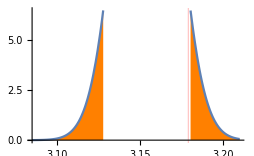

```mathematica
usaconfidenceinterval= Plot[PDF[NormalDistribution[3.15412,0.0159898],x]//Evaluate,{x,3.085,3.21},Filling-> Axis,FillingStyle->Orange,PlotRange->All,RegionFunction-> (#>3.18042||#<3.12782&),GridLines-> {{{3.179,Red}},None}]
```

```mathematica
(*plot the normal distribution for the US, using the SE*)
```

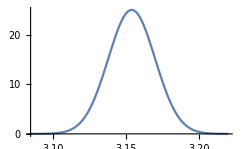

```mathematica
usanormal= Plot[PDF[NormalDistribution[3.154,0.0159898],x]//Evaluate,{x,3.085,3.22},Filling-> None,PlotRange-> All]
```

```mathematica
(*combine the SE and confidence interval graphs*)
```

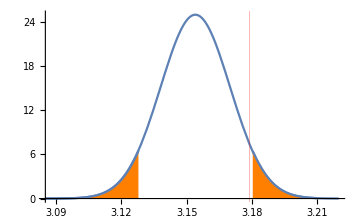

```mathematica
Show[usanormal,usaconfidenceinterval,GridLines->{{{3.179,Red}},None}]
```

```mathematica
usdata= {3.75,3.75,2.75,3,2.5,2.5,2.75,2.5,3,3.25,3,3.25,4,3.75,4,3,3,2.75,3.5,3,3.75,3,3.5,3.5,3.75,3.5,3.25,3.25,3.5,3.75,3.5,4,4,3.75,3.25,3.25,3.5,3.5,3.75,3.5,3.75,4,2.75,3.25,3.5,3.75,3.75,3.75,3.75,2.5,3,3.5,4,3.25,3.5,3.75,3.5,3.75,3.25,2.75,2.75,2.75,2.75,3.5,3.25,3.5,2.5,2.5,2.5,3.25,3.5,3.25,3.75,2.75,3,3,3,3.5,3.25,3.5,3,3.5,3.75,3,2.75,2.75,3,3.5,2.75,3.5,3,3.5,3.75,2.75,2.75,3.5,3.75,3.75,3.75,4,3,3.25,3.5,3.5,3,3.25,3.5,2.75,3.25,3.25,3,2.75,3.25,3.5,3.25,3.25,2.5,2.5,2.5,2.75,2.25,3.5,3.75,3,3.75,3.25,2.5,2.75,3,3,3.25,4,3.5,3.75,3.5,3.5,3.5,2.75,3,3.5,2.5,3.25,3.25,2.75,3,2.5,2.75,2.75,3,3.25,3.5,3.75,3.75,2.5,2.5,2.5,2.75,3,3,3,3.25,2.75,2.75,2.5,2.5,3,2.75,3.5,3,3.5,2.75,3.25,3.75,2.75,3.75,3,3.5,3.5,2.75,3.75,2.75,3.25,3.5,3.5,3,3.25,3.75,3.25,3.25,3.25,2.75,3,3.25,3.25,3,3.25,3,3.25,2.5,2.75,2.75,3.25,2.5,3,3,3,3,3,2.75,3.5,3.5,3.75,3.5,3.75,3.5,3.25,3.5,2.75,2.75,2.75,3,2.75,3,3.25,3.75,3.25,3.5,3.5,3.25,3.25,4,2.75,3.25,2.75,2,3.5,2.75,3,2.5,2.5,2.5,2.75,2.5,3,3.5,3.75,2.75,2.25,3,3.25,2.5,3.5,3.5,3,3.25,3.5,2.5,3.5,2,3.5,3.5,3,3.5,3.5,3.5,3.25,3.75,3.75,4,3.5,3.5,4,4,3,2.75,3.25,3.5,3.5,2.75,3.25,3,3.25,4,2.75,3,3.25,3.5,3.75,4,3.75,3,3.75,3,2.5,3.25,3,2.5,3.5,3,2.75,3.25,3.25,3.75,2.75,2.75,3.25,3.5,2.75,3.25,3.25,3,3,3,3.5,3,3,3.5,3.5,3,2.5,3.5,3.5,3.5,3,3.25,3,3.5,3.5,3.25,3.5,3.5,3,3.75,3.75,3.5,3.5,3.5,3.75,4,2.75,3.5,2.75,3,3,3.25,3.25,3.25,2.75,3,3.5,2.25,3.25,3.25,3.5,2.75,2,3.5,3.5,4,3.75,3,2.5,2.75,3,3.25,3.25,3.25,3.25,3.25,2.75,3.75,3.75,2.5,3,2.5,3,3.25,4,3.75,3.75,3.25,3.75,3,3.5,3,2.5,3.5,3,3,3,3.5,3.25,3.25,3.25,3.5,3,3.25,3.5,3.5,3.5,3.5,3.75,2.75,3,3.5,3.75,3.25,3.75,3,3,3.5,2,3.5,2.75,3.5,2.75,2.75,3.25,3.25,3.5,2.5,2.75,2.75,3.5,2.75,2.5,2.5,2.75,3.75,3.5,3.75,3.75,3.25,2.75,3,3.25,3.25,3.5,3.5,3.5,2.75,3.5,3.5,2.75,3,3.5,3,3,3.25,3.5,2.25,2.5,3,3.25,3.75,3.5,2.5,2.75,3.5,3,3,2.75,3.5,2.75,3,3.25,3.75,2.75,3,3.25,3.25,3.25,3.25,3.5,3,2.5,2.75,3,3,3.5,3.5,3.5,3.75,3.75,3.25,3.5,2.5,3.25,1.5,2,2.5,2.5,3.5,2.75,2.75,3.25,3,2.75,3,2.75,3.25,3.5,3.5,2.75,2.75,2.75,3,3.5,2.25,2.5,2.5,3.5,2.25,2.75,3,3,2.75,3.5,3,3,3.25,3,3,3.75,2.75,3,3.5,3.75,2.5,2.75,3,3,3,2.75,3,3,3,3.5,3.25,3.5,3,3.5,3.75,4,3.5,3.5,4,4,3,2.5,2.5,2.75,2.75,2.75,3.25,3.25,2.5,3.25,3.5,2.5,2.75,3.75,3.75,3.5,3,2.75,3.5,3.75,3,2.75,3.25,3.5,2.5,3.25,3.5,3.75,3.5,3.5,3.75,3,4,3.25,3.5,3.5,3.75,3.75,3.25,3.75,3.5,3.5,4,3.75,3.75,3,3.75,3.5,2.75,2.75,2.75,3,2.75,3.25,4,3.75,3.5,3.75,3.75,4,3.75,3,3,3,3.75,3,2,3.5,2,2,3,3.25,3.5,2.75,3.5,3,3.25,2,2.5,2.5,2.75,3,1.5,3,3.25,3.5,3,3,3,3,3.25,3.25,3.5,3.25,3.5,3,3,3.25,3.75,3.5,2.75,3,2.25,3,3,3,3,3,3.5,3.5,2.5,2.5,2.75,2.75,3.25,2.75,2.75,2.5,3,3,3.25,2.75,3,2,3.25,2.75,3,2.5,2.5,2.75,2.5,2.75,3,3,3.5,3.25,2,3.25,2.75,3,3.25,2.75,3,3.25,3.5,2.75,3.75,3.75,3.25,3.5,3.75,3.25,3.75,3.75,3.25,3.5,2.5,3,2,3,3,2.75,3,3,2.75,3.5,3.5,3.25,2.5,2.75,3,2.75,3,3,3.25,2.5,2.75,3.25,3.25,3.25,3.5,3.5,3.75,3.25,3,2,2,3,3,2.75,3,3,3.25,2.75,2.5,2.5,3,3,3.5,3.75,3,3.25,3.5,2.5,3,3.25,4,3.5,2.75,2.5,3,3.25,3.25,3.25,3.5,3}
```

```mathematica
(*plot the normal distribution for the US, using the SD*)
```

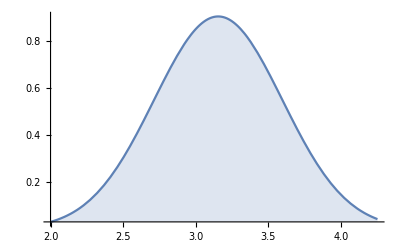

```mathematica
usasdnormal= Plot[PDF[NormalDistribution[3.154,0.441966],x]//Evaluate,{x,2,4.25},Filling-> Axis,PlotRange-> All]
```

```mathematica
(*combine the histogram and normal distribution using the standard error*)
```

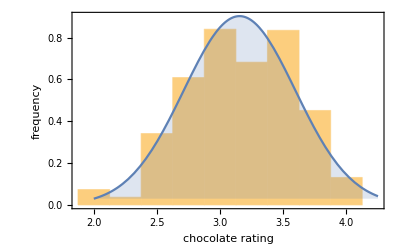

```mathematica
Show[Histogram[usdata,{Min[usdata]+0.25/2,Max[usdata]+0.25/2,0.25},"PDF"],usasdnormal,PlotRange->All,FrameLabel-> {"chocolate rating","frequency"},Frame->True]
```

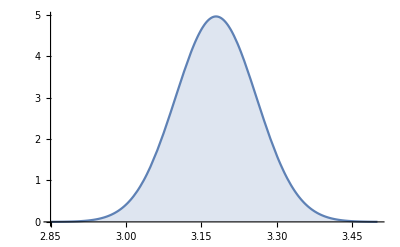

```mathematica
germanynormal= Plot[PDF[NormalDistribution[3.179,0.0804],x]//Evaluate,{x,2.85,3.5},Filling-> Axis, PlotRange -> All]
```

```mathematica
(*plotting the normal distribution for Germany using the SD*)
```

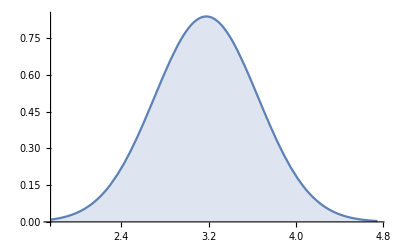

```mathematica
germanysdnormal= Plot[PDF[NormalDistribution[3.179,0.47577888374589244],x]//Evaluate,{x,1.75,4.75},Filling-> Axis, PlotRange -> {All,{0,All}}]
```

```mathematica
(*defining the dataset for germany*)
```

```mathematica
germanydata={2.75,3,3.5,3,3.25,3.25,3.5,1.5,3.75,3.5,3.25,3,2.5,3,3.25,3.25,3,3.25,3.5,3.75,3,3,3,3,3.25,4,3.5,3.5,3.5,2.5,2.75,2.5,3.75,3.5,3.75}
```

```mathematica
(*plotting the normal distribution using the SD on top of the histogram for Germany*)
```

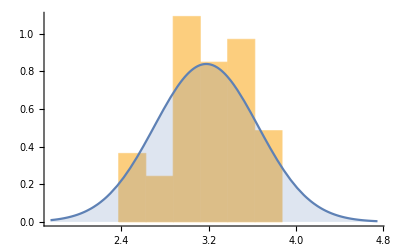

```mathematica
Show[Histogram[germanydata,{Min[germanydata]+0.25/2,Max[germanydata]+0.24/2,0.25},"PDF"],germanysdnormal,PlotRange-> All]
```

```mathematica
(*combine the normal distributions for Germany and the US*)
```

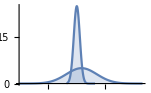

```mathematica
Show[germanynormal,usanormal]
```

```mathematica
(*plotting the t-distribution of the difference of means, pt 1*)
```

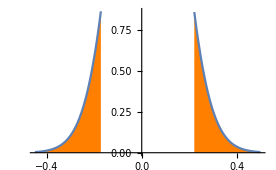

```mathematica
differenceofmeans=Plot[PDF[StudentTDistribution[0.02445,0.119047,34],x]//Evaluate,{x,-0.45,0.5},Filling-> Axis,FillingStyle-> Orange, PlotRange -> {All,{0,All}},RegionFunction->(#<-0.1720292||#>0.221372&)]
```

```mathematica
(*plot the t-distribution of the difference of means, pt 2*)
```

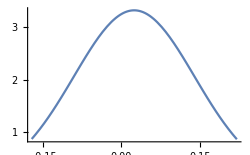

```mathematica
differenceofmeansconfidenceinterval=Plot[PDF[StudentTDistribution[0.02445,0.119047,34],x]//Evaluate,{x,-0.1720292,0.221372},Filling->None,RegionFunction->(#>-0.1720292||#<0.221372&),PlotRange->{All,{0,All}}]
```

```mathematica
(*combine the two graphs to illustrate the confidence interval*)
```

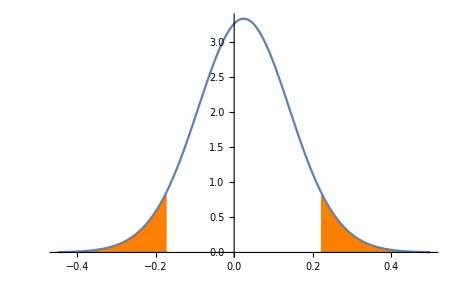

```mathematica
Show[differenceofmeans,differenceofmeansconfidenceinterval]
```

```mathematica
(*plotting the nulldistribution for the chocolate ratings)
```

```mathematica
nulldistribution=Plot[PDF[StudentTDistribution[0,0.119047,34],x]//Evaluate,{x,-0.45,0.5}, PlotRange -> {All,{0,All}},Filling-> None,GridLines-> {{{-0.195832,Black},{0.195832,Black},{0.02445,Red}},None}]
```

-Graphics-

```mathematica
(*plotting the desired effectsize distribution*)
```

```mathematica
effectsizedistribution=Plot[PDF[StudentTDistribution[0.2,0.119047,34],x]//Evaluate,{x,-0.25,0.65}, PlotRange -> {All,{0,All}},Filling-> None]
```

-Graphics-

```mathematica
(*plotting the proportion of the effectsize distribution that would be detected by test
```

```mathematica
powereffectsizedistribution=Plot[PDF[StudentTDistribution[0.2,0.119047,34],x]//Evaluate,{x,-0.25,0.65}, PlotRange -> {All,{0,All}},Filling-> Axis,FillingStyle-> Orange,RegionFunction->(#>0.195832&)]
```

-Graphics-

```mathematica
(*combining the different graphs*)
```

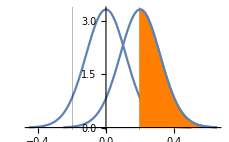

```mathematica
Show[effectsizedistribution,nulldistribution,powereffectsizedistribution,GridLines-> {{{-0.195832,Black},{0.195832,Black}},None}]
```

```mathematica
(*probability of a chocolate bar with more than 3.25 rating*)
```

```mathematica
Count[associateddata,u_/;u>3.25,Infinity]/Count[associateddata,u_/;u>0,Infinity]
```

```mathematica
702/1795
```

```mathematica
(*probaibility of >3,25 and US*)
Count[usdata,u_/;u>3.25,Infinity]/Count[associateddata,u_/;u>0,Infinity]
```

54/359

```mathematica
(*conditional probability of >3.25, given US*)
```

```mathematica
(Count[usdata,u_/;u>3.25,Infinity]/Count[associateddata,u_/;u>0,Infinity])/(Count[usdata,u_/;u>0,Infinity]/Count[associateddata,u_/;u>0,Infinity])
```

135/382

```mathematica
(*conditional probability of >3.25, given Germany)
```

```mathematica
(Count[germanydata,u_/;u>3.25,Infinity]/Count[associateddata,u_/;u>0,Infinity])/(Count[germanydata,u_/;u>0,Infinity]/Count[associateddata,u_/;u>0,Infinity])
```

13/35